```mathematica
Quit
```

#### diagsimp + amp

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/marco/Documents/università/Dimension6/notebooks/haz final/HAZ D6 Uni

```mathematica
<<Hggdiagsimp.m
```

Remove::rmnsm: There are no symbols matching "Tracer`Private`*".

T R A C E R

=============

A MATHEMATICA PACKAGE FOR GAMMA-ALGEBRA IN ARBITRARY DIMENSIONS

by M. Jamin and M.E. Lautenbacher

Physics Dept. T31, Technical University Munich

Version 1.1.1 from Mon Dec 30 15:36:00 MET 1991

(based on MATHEMATICA Version 1.2)

The package defines the following commands:

"AntiCommute", "ContractEpsGamma", "Eps", "G",
"GammaTrace", "G5", "H",
"ListCommands", "NoSpur",
"OnShell", "OutputFormat", "RemoveHatMomenta",

"RemoveNCM", "S", "Sigma", "SortLine", "Spur", "T",
"ToDiracBasis",
"ToHatTilde", "ToOtimes", "ToUG5", "U",
"VectorDimension", "Version".

                                    Help on usage as usual per ?Name.

DEFAULT SETTINGS ON STARTUP:

----------------------------

NonCommutativeMultiply will be removed.

Current OutputFormat is set to "texlike".

Package uses a non anticommuting G5 in "d" dimensions.

Dimension set to "nd". Used type of G5 left unchanged.

Package uses the usual anticommuting G5 in "nd" dimensions.

WARNING: Use of the Epsilon tensor in d != 4 dimensions with
         anticommuting G5 is algebraically inconsistent.

The gamma matrix line(s) "lferm" will be traced.

1

2

3

4

5

6

7

8

9

10

11

```mathematica
<<Hggamp.m
```

Diagrams

1

2

3

4

5

6

7

8

9

10

11

Computing color factors

XXXXXXXXXXX

Color factors computed

Color factor of diag 1:    1

Color factor of diag 2:    1

Color factor of diag 3:    1

Color factor of diag 4:    1

Color factor of diag 5:    1

Color factor of diag 6:    1

Color factor of diag 7:    1

Color factor of diag 8:    1

Color factor of diag 9:    1

Color factor of diag 10:    1

Color factor of diag 11:    1

N° of diag in amp3: 11

N° of diag in amp2: 10

diag n. 1 in amp2 correspond to diag n. {{5}} in amp3

diag n. 2 in amp2 correspond to diag n. {{7}} in amp3

diag n. 3 in amp2 correspond to diag n. {{3}} in amp3

diag n. 4 in amp2 correspond to diag n. {{10}} in amp3

diag n. 5 in amp2 correspond to diag n. {{9}} in amp3

diag n. 6 in amp2 correspond to diag n. {{11}} in amp3

diag n. 7 in amp2 correspond to diag n. {{4}} in amp3

diag n. 8 in amp2 correspond to diag n. {{8}} in amp3

diag n. 9 in amp2 correspond to diag n. {{6}} in amp3

diag n. 10 in amp2 correspond to diag n. {{1},{2}} in amp3

N° of diag in amp2: 10;   order of diag compared to amp3: {{{5}},{{7}},{{3}},{{10}},{{9}},{{11}},{{4}},{{8}},{{6}},{{1},{2}}}

If everything has been done correctly, a zero must happear here: 0

```mathematica
Beep[]
```

```mathematica
Quit
```

#### PV

```mathematica
Needs["FeynCalc`"];
```

FeynCalc 9.1.0 (development version). For help, use the documentation center, check out the wiki or write to the mailing list.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput. Phys. Commun., 207C, 432-444, 2016, arXiv:1601.01167

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun., 64, 345-359, 1991.

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/marco/Documents/università/Dimension6/notebooks/haz final/HAZ D6 Uni

```mathematica
<<Hggamp.res;
<<Utils.m;
```

```mathematica
prepareDiag[exp_]:=Module[{temp,check,total},temp=exp;
total=0;
temp=temp/.sp[a_,b_]->SPD[a,b]/.pp[p___,m_]->FAD[{p,m}]/.nd->D;
Return[temp];];
```

```mathematica
Kinetic1:={Pair[Momentum[Ep1],Momentum[q1]]->0,
Pair[Momentum[Ep2],Momentum[q2]]->0
}
Kinetic2:={Pair[Momentum[Ep1],Momentum[q1]]->0,
Pair[Momentum[Ep2],Momentum[q2]]->0,
sp[Ep1,q1]->0,
sp[Ep2,q2]->0,
sp[Ep2,q1] sp[Ep1,q2]->Subscript[A, αβ]^hγγ/4+sp[Ep1,Ep2] sp[q1,q2],
sp[Ep1,Ep2]->g^αβ,
sp[q1,q1]->AA,
sp[q2,q2]->z,
sp[q1,q2]->(h-z)/2,
MZ->√z,
MW->√w,
MH->√h,
GaugeXi[Q]->ξ,
e->g1 cw,
cw->gw/(√(g1^2+gw^2))
}
```

```mathematica
B0simplify:={A0[m_]->-m Log[m]+m,
B0[q_,m_,0]->B0[q,0,m],
B0[a_,0,a_]->-Log[a]+2,
B0[0,m_,m_]->-Log[m],
B0[0,m1_,m2_]->1+(m2 Log[m2]-m1 Log[m1])/(m1-m2),
B0[AA,m_,m_]->-Log[m],
B0[AA,m1_,m2_]->1+(m2 Log[m2]-m1 Log[m1])/(m1-m2)}
```

```mathematica
diagprep=LAMBDA^2/(e^2 vev)*prepareDiag[diag]/.v2flag->1/.cB->-cγZ gw/g1+cW gw^2/g1^2-cWB (gw^2-g1^2)/(2 g1^2);
```

```mathematica
diagfin={};
Do[
temp=diagprep[[i]];
temp=OneLoop[p,-I/Pi^2 temp,OneLoopSimplify->True]/.Kinetic1;
temp=PaVeReduce[temp,PaVeAutoReduce->True]/.Pair[Momentum[a_],Momentum[b_]]->sp[a,b]//.Kinetic2/.D->4-2 ϵ/.B0[x_,m1_,m2_]->1/ϵ + B0[x,m1,m2]/.A0[m_]->m/ϵ-m Log[m]+m;
temp=temp//.B0simplify;
temp=Limit[temp,AA->0,Analytic->True];
temp=Normal[Series[temp,{ϵ,0,0}]];
temp = Collect[temp,{ϵ,Subscript[A, αβ]^hγγ,g^αβ,B0[___],C0[___]},Simplify];
NotebookDelete[print];print=PrintTemporary[i,"/",Length[diagprep]];
diagfin=Append[diagfin,temp],
{i,Length[diagprep]}];
result=Collect[Total[diagfin],{ϵ,cγZ,cW,cWB,vev,Subscript[A, αβ]^hγγ,g^αβ,B0[___],C0[___]},Simplify];
```

$Aborted

```mathematica
Beep[]
```

```mathematica
FILE=NotebookDirectory[]<>"Result.res";
DeleteFile[FILE];OpenWrite[FILE];
WriteString[FILE,"diagfin=\n"];
Write[FILE,diagfin];
WriteString[FILE,"result=\n"];
Write[FILE,result];
Close[FILE];
```

```mathematica
Quit
```

#### Results

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/marco/Documents/università/Dimension6/notebooks/haz final/HAZ D6

```mathematica
<<Hggamp.res;
<<Result.res;
<<H_WF.res;
<<dv.res;
<<haast.res;
<<ResultAZ.res;
<<ResultZZ.res;
```

```mathematica
Kinetic1:={Pair[Momentum[Ep1],Momentum[q1]]->0,
Pair[Momentum[Ep2],Momentum[q2]]->0
}
Kinetic2:={Pair[Momentum[Ep1],Momentum[q1]]->0,
Pair[Momentum[Ep2],Momentum[q2]]->0,
sp[Ep1,q1]->0,
sp[Ep2,q2]->0,
sp[Ep2,q1] sp[Ep1,q2]->Subscript[A, αβ]^hγγ/4+sp[Ep1,Ep2] sp[q1,q2],
sp[Ep1,Ep2]->g^αβ,
sp[q1,q1]->AA,
sp[q2,q2]->z,
sp[q1,q2]->(h-z)/2,
MZ->√z,
MW->√w,
MH->√h,
GaugeXi[Q]->ξ,
e->g1 cw,
cw->gw/(√(g1^2+gw^2))
}
```

```mathematica
B0simplify:={A0[m_]->-m Log[m]+m,
B0[q_,m_,0]->B0[q,0,m],
B0[a_,0,a_]->-Log[a]+2,
B0[0,m_,m_]->-Log[m],
B0[0,m1_,m2_]->1+(m2 Log[m2]-m1 Log[m1])/(m1-m2),
B0[AA,m_,m_]->-Log[m],
B0[AA,m1_,m2_]->1+(m2 Log[m2]-m1 Log[m1])/(m1-m2)}
```

```mathematica
resulte=Coefficient[result,ϵ,-1];
result0=Coefficient[result,ϵ,0];
```

```mathematica
resul0ZZcb=Coefficient[result0ZZ, g^αβ cB] Subscript[A, αβ]^hγγ;
resul0AZcb=Coefficient[-result0AZ/z, g^αβ cB] Subscript[A, αβ]^hγγ;
```

```mathematica
resul0cw=Coefficient[result0,cW];
resul0ZZcw=Coefficient[result0ZZ, g^αβ cW] Subscript[A, αβ]^hγγ;
resul0AZcw=Coefficient[-result0AZ/z, g^αβ cW] Subscript[A, αβ]^hγγ;
```

```mathematica
resul0cwb=Collect[Coefficient[result0/.w->gw^2 vev^2/4/.z->(g1^2+gw^2)vev^2/4/.h->2lam vev^2,cWB],{Subscript[A, αβ]^hγγ,B0[___],C0[___],Log[___]},Simplify]//.gw^2 vev^2->4w//.(g1^2+gw^2)vev^2->4z//.lam vev^2->h/2;
resul0ZZcwb=Coefficient[result0ZZ, g^αβ cWB] Subscript[A, αβ]^hγγ;
resul0AZcwb=Coefficient[-result0AZ/z, g^αβ cWB] Subscript[A, αβ]^hγγ;
resul0AAstcwb=vev gw/g1 haast;
```

```mathematica
resul0cγz=Coefficient[result0,cγZ];
```

#### cB finite part

```mathematica
ResultCB=Collect[resul0ZZcb+resul0AZcb/.EL->(g1 gw)/(√(g1^2+gw^2))/.w->gw^2 vev^2/4/.z->(g1^2+gw^2)vev^2/4//Expand,{Subscript[A, αβ]^hγγ,ϵ,B0[___],Log[___]},Simplify]//.gw^2 vev^2->4w//.(g1^2+gw^2) vev^2->4z;
FreeQ[ResultCB,ξ]
```

True

#### cW finite part

```mathematica
ResultCW=Collect[resul0cw+resul0ZZcw+resul0AZcw/.EL->(g1 gw)/(√(g1^2+gw^2))/.w->gw^2 vev^2/4/.z->(g1^2+gw^2)vev^2/4//PowerExpand,{Subscript[A, αβ]^hγγ,ϵ,C0[___],B0[___],Log[___]},Simplify]//.gw^2 vev^2->4w//.(g1^2+gw^2) vev^2->4z;
FreeQ[ResultCW,ξ]
```

True

#### cWB finite part

```mathematica
ResultCWB=Collect[PowerExpand[resul0cwb+resul0AAstcwb+resul0ZZcwb+resul0AZcwb]/.EL->(g1 gw)/(√(g1^2+gw^2))/.w->gw^2 vev^2/4/.z->(g1^2+gw^2)vev^2/4,{Subscript[A, αβ]^hγγ,ϵ,C0[___],B0[___],Log[___],ξ},Simplify]//.gw^2 vev^2->4w//.(g1^2+gw^2) vev^2->4z
FreeQ[ResultCWB,ξ]
```

(-((-55 g1^16 vev^10-2 g1^14 vev^8 (24 h+318 t+55 (5 gw^2-4 lam) vev^2)-4 g1^12 vev^6 (19 h^2+12 h (16 t+(9 gw^2-8 lam) vev^2)+vev^2 (-1272 lam t+521 gw^4 vev^2+gw^2 (1511 t-1134 lam vev^2)))-2 g1^10 vev^4 (96 h^3+8 h^2 (15 t+38 (gw^2-lam) vev^2)+gw^2 vev^4 (-26240 lam t+2495 gw^4 vev^2+2 gw^2 (5279 t-3610 lam vev^2))+24 h vev^2 (-128 lam t+25 gw^4 vev^2+64 gw^2 (2 t-lam vev^2)))+2 g1^8 vev^2 (96 h^4-96 h^3 (16 t+(7 gw^2-8 lam) vev^2)+gw^4 vev^4 (4096 t^2+2 (-11967 gw^2+37048 lam) t vev^2+gw^2 (-3089 gw^2+8996 lam) vev^4)-2 h^2 vev^2 (-480 lam t+537 gw^4 vev^2+20 gw^2 (37 t-82 lam vev^2))-24 gw^2 h vev^4 (-896 lam t+25 gw^4 vev^2+136 gw^2 (2 t-lam vev^2)))+2 g1^2 gw^2 (-49152 h^4 lam t+915 gw^12 vev^10+2 gw^10 vev^8 (252 h+6099 t-2362 lam vev^2)+8 gw^6 h vev^4 (132 h^2+2653 h t-414 h lam vev^2-4224 lam t vev^2)-768 gw^2 h^3 (2 h t-h lam vev^2+16 lam t vev^2)-64 gw^4 h^2 vev^2 (9 h^2-144 h t-1280 t^2+72 h lam vev^2+362 lam t vev^2)+8 gw^8 vev^6 (169 h^2+32 t (80 t-193 lam vev^2)+384 h (2 t-lam vev^2)))+2 g1^6 (192 h^4 (8 t+(3 gw^2-4 lam) vev^2)+gw^6 vev^6 (28672 t^2+2 (-9109 gw^2+30016 lam) t vev^2+gw^2 (-1025 gw^2+1892 lam) vev^4)-8 gw^2 h^2 vev^4 (-3664 lam t+491 gw^4 vev^2+2 gw^2 (647 t-476 lam vev^2))+24 gw^4 h vev^6 (1280 lam t+5 gw^4 vev^2-64 gw^2 (2 t-lam vev^2))+192 h^3 vev^2 (64 lam t-5 gw^4 vev^2+24 gw^2 (-2 t+lam vev^2)))+4 g1^4 (-6144 h^4 lam t+567 gw^12 vev^10+gw^10 vev^8 (348 h+4099 t-2750 lam vev^2)+8 gw^6 h vev^4 (12 h^2-2797 h t+192 h lam vev^2-384 lam t vev^2)+1920 gw^2 h^3 (2 h t-h lam vev^2+16 lam t vev^2)+gw^8 vev^6 (-993 h^2+8 t (2816 t-1555 lam vev^2)+1248 h (2 t-lam vev^2))+64 gw^4 h^2 vev^2 (3 h^2+24 h (-2 t+lam vev^2)+2 t (64 t+313 lam vev^2)))+gw^4 (gw^2-8 lam) (4 h^2 (844 gw^4 t vev^4+109 gw^6 vev^6)+240 h (16 gw^6 t vev^6+gw^8 vev^8)-960 h^4 (16 t+4 w)+gw^8 vev^8 (3724 t+1156 w)+960 h^3 (gw^4 vev^4+64 t w)))/(72 g1 gw (g1^2+gw^2) (g1^2+5 gw^2) (g1^2+gw^2-8 lam) vev^4 (4 h^2+(g1^2+gw^2)^2 vev^4) (16 t+4 z)))-(g1 gw^3 ξ)/(g1^2+gw^2-8 lam)+(64 g1 gw^3 t B0[h,t,t])/(9 (g1^2+gw^2-8 lam)^2 vev^2)+1/(2 g1 gw (g1^2+gw^2-8 lam)^2)(g1^6 (gw^2+4 lam)+g1^4 (-13 gw^4+16 gw^2 lam-64 lam^2)-gw^2 (gw^6-96 gw^2 lam^2+256 lam^3)+g1^2 (-3 gw^6+28 gw^4 lam-96 gw^2 lam^2+256 lam^3)) B0[h,w,w]+((4 g1 gw (g1^2+gw^2) lam)/((g1^2+gw^2-8 lam)^2)+(g1 gw^3 (g1^2+gw^2) ξ)/((g1^2+gw^2-8 lam)^2)) B0[h,w ξ,w ξ]+((g1^2-gw^2) (64 h^4+44 (g1^2+gw^2)^2 h^2 vev^4-14 (g1^2+gw^2)^3 h vev^6+3 (g1^2+gw^2)^4 vev^8-224 h^3 z) B0[z,h,z])/(24 g1 gw (g1^2+gw^2) vev^4 (4 h^2+(g1^2+gw^2)^2 vev^4))+((-17 g1^14 vev^4+g1^12 (-136 t vev^2+(-125 gw^2+272 lam) vev^4)+g1^10 (224 t^2-32 (67 gw^2-68 lam) t vev^2+(-297 gw^4+1728 gw^2 lam-1088 lam^2) vev^4)+g1^4 gw^2 (-804864 lam^2 t^2+129 gw^8 vev^4-4096 gw^2 lam t (-18 t+11 lam vev^2)+8 gw^6 (5 t vev^2-138 lam vev^4)-64 gw^4 (199 t^2+100 lam t vev^2-18 lam^2 vev^4))+g1^6 (14336 lam^2 t^2-11 gw^8 vev^4-1024 gw^2 lam t (-193 t+117 lam vev^2)-128 gw^6 (29 t vev^2-10 lam vev^4)-64 gw^4 (393 t^2-644 lam t vev^2+98 lam^2 vev^4))+g1^2 gw^4 (509952 lam^2 t^2+69 gw^8 vev^4+3072 gw^2 lam t (-43 t+23 lam vev^2)+32 gw^6 (23 t vev^2-30 lam vev^4)+32 gw^4 (11 t^2-588 lam t vev^2+102 lam^2 vev^4))-g1^8 (269 gw^6 vev^4+512 lam t (7 t+17 lam vev^2)+56 gw^4 (91 t vev^2-54 lam vev^4)+32 gw^2 (379 t^2-1004 lam t vev^2+182 lam^2 vev^4))+9 gw^6 (gw^2-8 lam)^2 (32 t^2+gw^4 vev^4+32 t w)) B0[z,t,t])/(72 g1 gw (g1^2+gw^2)^2 (g1^2+gw^2-8 lam)^2 vev^2 (16 t+4 z))+((-g1^14+g1^12 (-35 gw^2+16 lam)+g1^2 gw^8 (-583 gw^4+18304 gw^2 lam-105280 lam^2)-g1^10 (5 gw^4+128 gw^2 lam+64 lam^2)+3 gw^10 (121 gw^4-1456 gw^2 lam+3904 lam^2)+g1^8 (625 gw^6-560 gw^4 lam+1728 gw^2 lam^2)+g1^6 (-179 gw^8+11008 gw^6 lam+7040 gw^4 lam^2)+g1^4 (-1721 gw^10+34096 gw^8 lam-50304 gw^6 lam^2)) B0[z,w,w])/(48 g1 gw (g1^2+gw^2)^2 (g1^2+5 gw^2) (g1^2+gw^2-8 lam)^2)+(-(4 g1 gw (g1^2+gw^2) lam)/((g1^2+gw^2-8 lam)^2)-(g1 gw^3 (g1^2+gw^2) ξ)/((g1^2+gw^2-8 lam)^2)) B0[z,w ξ,w ξ]-(8 g1 gw^3 t (16 t+(g1^2+gw^2-8 lam) vev^2) C0[0,z,h,t,t,t])/(9 (g1^2+gw^2) (g1^2+gw^2-8 lam) vev^2)+(gw (-2 g1^8+g1^6 (gw^2+16 lam)+g1^4 (23 gw^4-40 gw^2 lam)-g1^2 (gw^6-16 gw^4 lam)+3 (gw^8-8 gw^6 lam)) vev^2 C0[0,z,h,w,w,w])/(8 g1 (g1^2+gw^2) (g1^2+gw^2-8 lam))+(-(2 g1 gw^3 lam vev^2 ξ)/(g1^2+gw^2-8 lam)-(g1 gw^5 vev^2 ξ^2)/(2 (g1^2+gw^2-8 lam))) C0[0,z,h,w ξ,w ξ,w ξ]-((g1^2-gw^2) h (-32 h^3-16 (g1^2+gw^2)^2 h vev^4+(g1^2+gw^2)^3 vev^6+80 h^2 z) Log[h])/(12 g1 gw (g1^2+gw^2) vev^4 (4 h^2+(g1^2+gw^2)^2 vev^4))+(t (36 gw^6 t+17 g1^8 vev^2-9 gw^8 vev^2-4 g1^4 (393 gw^2 t+10 gw^4 vev^2)+6 g1^2 (166 gw^4 t+9 gw^6 vev^2)+g1^6 (28 t-344 w)) Log[t])/(9 g1 gw (g1^2+gw^2)^2 vev^2 (16 t+4 z))+((25 g1^8 gw+202 g1^6 gw^3+212 g1^4 gw^5-346 g1^2 gw^7+99 gw^9) Log[w])/(24 (g1^2+gw^2)^2 (g1^3+5 g1 gw^2))+((g1^2-gw^2) (-32 h^3-24 (g1^2+gw^2)^2 h vev^4+7 (g1^2+gw^2)^3 vev^6+112 h^2 z) Log[z])/(48 g1 gw vev^2 (4 h^2+(g1^2+gw^2)^2 vev^4))) A_αβ^hγγ

False

```mathematica
rest =(-(g1 gw^3 ξ)/(g1^2+gw^2-8 lam)+((4 g1 gw (g1^2+gw^2) lam)/((g1^2+gw^2-8 lam)^2)+(g1 gw^3 (g1^2+gw^2) ξ)/((g1^2+gw^2-8 lam)^2)) B0[h,w ξ,w ξ]+(-(4 g1 gw (g1^2+gw^2) lam)/((g1^2+gw^2-8 lam)^2)-(g1 gw^3 (g1^2+gw^2) ξ)/((g1^2+gw^2-8 lam)^2)) B0[z,w ξ,w ξ]+(-(2 g1 gw^3 lam vev^2 ξ)/(g1^2+gw^2-8 lam)-(g1 gw^5 vev^2 ξ^2)/(2 (g1^2+gw^2-8 lam))) C0[0,z,h,w ξ,w ξ,w ξ])Subscript[A, αβ]^hγγ;
```

```mathematica
testCWB=Collect[ResultCWB-rest,{Subscript[A, αβ]^hγγ,ϵ,C0[___],B0[___],Log[___],ξ},Simplify];
FreeQ[testCWB,ξ]
```

True

```mathematica
Collect[Collect[rest,{ Subscript[A, αβ]^hγγ,C0[___],B0[___],Log[_]},Simplify]/.(g1^2+gw^2-8 lam)->4(z-h)/vev^2/. 4 lam+gw^2 ξ->2(h+2w ξ)/vev^2/.(g1^2+gw^2)vev^2->4z/.vev^2->4w/gw^2,{ Subscript[A, αβ]^hγγ,g1 gw,C0[___],B0[___]},Simplify]
```

g1 gw ((w ξ)/(h-z)+(z (h+2 w ξ) B0[h,w ξ,w ξ])/(2 (h-z)^2)-(z (h+2 w ξ) B0[z,w ξ,w ξ])/(2 (h-z)^2)+(w ξ (h+2 w ξ) C0[0,z,h,w ξ,w ξ,w ξ])/(h-z)) A_αβ^hγγ

```mathematica
Collect[Simplify[Coefficient[diagfin,Subscript[A, αβ]^hγγ cWB C0[0,z,h,w ξ,w ξ,w ξ]]/.w->gw^2 vev^2/4/.z->(g1^2+gw^2)vev^2/4/.h->2lam vev^2]/.(g1^2+gw^2-8 lam)->4(z-h)/vev^2,lam,Simplify]
Collect[Total[%]/.w->gw^2 vev^2/4/.z->(g1^2+gw^2)vev^2/4/.h->2lam vev^2,{ξ},Simplify]
-(2 g1 gw^3 lam vev^2 ξ)/(g1^2+gw^2-8 lam)+(g1 gw^5 vev^2 ξ^2)/(2 (g1^2+gw^2-8 lam))//Together
```

{0,(g1 gw^5 (g1^2-gw^2) vev^4 ξ^2)/(2 (g1^2+gw^2) (h-z)),(g1 gw^3 (g1^2-gw^2) lam vev^4 ξ)/((g1^2+gw^2) (-h+z))+(g1 gw^5 (g1^2-gw^2) vev^4 ξ^2)/(4 (g1^2+gw^2) (-h+z)),0,0,0,0,0,0,0,0,0,0,0,0,0,0,(g1 gw^3 lam vev^4 ξ)/(2 h-2 z),0,0,0,0,0,(g1 gw^3 lam vev^4 ξ)/(2 h-2 z),(2 g1 gw^5 lam vev^4 ξ)/((g1^2+gw^2) (-h+z))+(g1 gw^7 vev^4 ξ^2)/(2 (g1^2+gw^2) (h-z))}

-(g1 gw^5 vev^2 ξ^2)/(g1^2+gw^2-8 lam)

(g1 vev^2 (-4 gw^3 lam ξ+gw^5 ξ^2))/(2 (g1^2+gw^2-8 lam))

```mathematica
Total[{0,-(g1 gw^5 (g1^2-gw^2) vev^4 ξ^2)/(2 (g1^2+gw^2) (h-z)),(g1 gw^3 (g1^2-gw^2) lam vev^4 ξ)/((g1^2+gw^2) (-h+z))+(g1 gw^5 (g1^2-gw^2) vev^4 ξ^2)/(4 (g1^2+gw^2) (-h+z)),0,0,0,0,0,0,0,0,0,0,0,0,0,0,(g1 gw^3 lam vev^4 ξ)/(2 h-2 z),0,0,0,0,0,(g1 gw^3 lam vev^4 ξ)/(2 h-2 z),(2 g1 gw^5 lam vev^4 ξ)/((g1^2+gw^2) (-h+z))+(g1 gw^7 vev^4 ξ^2)/(2 (g1^2+gw^2) (h-z))}]//Simplify
```

(g1 gw^5 (-3 g1^2+5 gw^2) vev^4 ξ^2)/(4 (g1^2+gw^2) (h-z))

```mathematica
lista[[2]]
lista[[3]]
lista[[18]]
lista[[24]]
lista[[25]]
```

{{3},{4},{5},{6}}

{{1},{2}}

{{9},{10}}

{{22},{23}}

{{7},{8}}

```mathematica
diagfin[[2]]
diagfin[[3]]
diagfin[[18]]
diagfin[[24]]
diagfin[[25]]
```

(2 cWB g^αβ g1 gw^3 (-g1^2+gw^2) vev^2 ξ)/((g1^2+gw^2) ϵ)+(2 cWB g^αβ g1 gw^3 (-g1^2+gw^2) vev^2 ξ B0[h,w ξ,w ξ])/(g1^2+gw^2)+((cWB g1 gw^3 (g1^2-gw^2) vev^2 ξ)/((g1^2+gw^2) (h-z))+(cWB g1 gw^3 (g1^2-gw^2) vev^2 z ξ B0[h,w ξ,w ξ])/((g1^2+gw^2) (h-z)^2)+(cWB g1 gw^3 (-g1^2+gw^2) vev^2 z ξ B0[z,w ξ,w ξ])/((g1^2+gw^2) (h-z)^2)+(2 cWB g1 gw^3 (g1^2-gw^2) vev^2 w ξ^2 C0[0,z,h,w ξ,w ξ,w ξ])/((g1^2+gw^2) (h-z))) A_αβ^hγγ

(cWB g^αβ g1 gw (g1^2-gw^2) vev^2 (4 lam+gw^2 ξ))/((g1^2+gw^2) ϵ)+(cWB g^αβ g1 gw (g1^2-gw^2) vev^2 (4 lam+gw^2 ξ) B0[h,w ξ,w ξ])/(g1^2+gw^2)+(-(cWB g1 gw (g1^2-gw^2) vev^2 (4 lam+gw^2 ξ))/(2 (g1^2+gw^2) (h-z))-(cWB g1 gw (g1^2-gw^2) vev^2 z (4 lam+gw^2 ξ) B0[h,w ξ,w ξ])/(2 (g1^2+gw^2) (h-z)^2)+(cWB g1 gw (g1^2-gw^2) vev^2 z (4 lam+gw^2 ξ) B0[z,w ξ,w ξ])/(2 (g1^2+gw^2) (h-z)^2)-(cWB g1 gw (g1^2-gw^2) vev^2 w ξ (4 lam+gw^2 ξ) C0[0,z,h,w ξ,w ξ,w ξ])/((g1^2+gw^2) (h-z))) A_αβ^hγγ

g^αβ ((cWB g1 gw^3 vev^2 (h^2+w^2 (-1+ξ)^2-2 h w (1+ξ)) B0[h,w,w ξ])/(4 h w)-(cWB g1 gw^3 h vev^2 B0[h,w ξ,w ξ])/(4 w)+(cWB g1 gw (24 w z (-z+w (-1+ξ))+gw^2 vev^2 (z^2-2 w z (-5+ξ)+w^2 (-1+ξ)^2)) B0[z,w,w ξ])/(12 w z)-(cWB g1 gw^3 vev^2 (z-4 w ξ) B0[z,w ξ,w ξ])/(12 w)+1/(12 h z)cWB g1 gw (-(24 h w z+gw^2 vev^2 (h (-6 z+w (-1+ξ))+3 w z (-1+ξ))) (-1+ξ)+(-24 h w z+gw^2 vev^2 (-3 w z (-1+ξ)+h (w+4 z-w ξ))) Log[w]+(24 h w z+gw^2 vev^2 (h (-4 z+w (-1+ξ))+3 w z (-1+ξ))) ξ Log[w ξ]))+(-1/(8 h w (h-z)^2)cWB g1 gw (-4 h^3 w+gw^2 vev^2 w^2 z (-1+ξ)^2+h^2 (-4 w (z+w (-1+ξ))+gw^2 vev^2 (z+2 w (1+ξ)))-2 h w (2 w z (-1+ξ)+gw^2 vev^2 (w (-1+ξ)^2+z (1+ξ)))) B0[h,w,w ξ]+(cWB g1 gw^3 h vev^2 z B0[h,w ξ,w ξ])/(8 w (h-z)^2)+(cWB g1 gw (4 w (z (z-3 w (-1+ξ))+h (-3 z+w (-1+ξ)))+gw^2 vev^2 (h (z+w (3+ξ))-w (w (-1+ξ)^2+z (3+ξ)))) B0[z,w,w ξ])/(8 w (h-z)^2)-(cWB g1 gw^3 h vev^2 z B0[z,w ξ,w ξ])/(8 w (h-z)^2)+(cWB g1 gw ξ (4 w (h+z)-gw^2 vev^2 (h+w-w ξ)) C0[0,z,h,w ξ,w ξ,w])/(4 (h-z))+(cWB g1 gw^3 h vev^2 ξ C0[0,z,h,w ξ,w ξ,w ξ])/(4 h-4 z)+1/(8 h (h-z))cWB g1 gw (4 h^2-2 gw^2 h vev^2+8 h w-gw^2 vev^2 w+4 h z+2 gw^2 h vev^2 ξ-8 h w ξ+2 gw^2 vev^2 w ξ-gw^2 vev^2 w ξ^2+(-8 h w+gw^2 vev^2 (h+w-w ξ)) Log[w]+ξ (8 h w-gw^2 vev^2 (h+w-w ξ)) Log[w ξ])) A_αβ^hγγ+(-2 cWB g^αβ g1 gw z+1/2 cWB g1 gw A_αβ^hγγ)/ϵ

g^αβ (-(cWB g1 gw (gw^2 vev^2-4 z) (h^2+w^2 (-1+ξ)^2-2 h w (1+ξ)) B0[h,w,w ξ])/(4 h w)+(cWB g1 gw h (gw^2 vev^2-4 z) B0[h,w ξ,w ξ])/(4 w)-(cWB g1 gw (24 w z (-z+w (-1+ξ))+gw^2 vev^2 (z^2-2 w z (-5+ξ)+w^2 (-1+ξ)^2)) B0[z,w,w ξ])/(12 w z)+(cWB g1 gw^3 vev^2 (z-4 w ξ) B0[z,w ξ,w ξ])/(12 w)+1/(12 h z)cWB g1 gw ((12 z (h (2 w+z)-w z (-1+ξ))+gw^2 vev^2 (h (-6 z+w (-1+ξ))+3 w z (-1+ξ))) (-1+ξ)+(12 z (h (2 w+z)-w z (-1+ξ))+gw^2 vev^2 (h (-4 z+w (-1+ξ))+3 w z (-1+ξ))) Log[w]+ξ (-12 z (h (2 w+z)-w z (-1+ξ))+gw^2 vev^2 (-3 w z (-1+ξ)+h (w+4 z-w ξ))) Log[w ξ]))+(1/(8 g1 h w (h-z)^2)cWB gw (gw^4 h vev^2 (-h^2+h z-w z (-1+ξ))+g1^2 (2 h^4-h^3 (gw^2 vev^2+4 (w+z))+w^2 (gw^2 vev^2-2 z) z (-1+ξ)^2+2 h^2 (w^2+2 w z+z^2-w^2 ξ^2+gw^2 vev^2 w (1+ξ))-h w (gw^2 vev^2 (2 w (-1+ξ)^2+z (3+ξ))-4 z (2 z+w (2-3 ξ+ξ^2))))) B0[h,w,w ξ]+(cWB gw h (gw^4 vev^2 (h-z)+g1^2 (-2 h^2+gw^2 h vev^2+4 h z-2 z^2)) B0[h,w ξ,w ξ])/(8 g1 w (h-z)^2)+1/(16 g1 w (h-z)^2)cWB gw (-gw^4 vev^2 (h-z) (z+w (-1+ξ))+g1^2 (8 w (h-3 z) (w+z-w ξ)+gw^2 vev^2 (z^2-w z (-9+ξ)+2 w^2 (-1+ξ)^2+h (z-w (5+3 ξ))))) B0[z,w,w ξ]-(cWB gw^3 vev^2 z (gw^2 (-h+2 w+z-2 w ξ)+g1^2 (h+2 w+z-2 w ξ)) B0[z,w ξ,w ξ])/(16 g1 w (h-z)^2)+(cWB gw (gw^4 vev^2 (-h+z)+g1^2 (gw^2 vev^2 (h-3 z+2 w (-1+ξ))+8 (z (z-w (-2+ξ))+h (-z+w ξ)))) C0[0,z,h,w,w,w ξ])/(8 g1 (h-z))-(cWB gw^3 (g1^2+gw^2) vev^2 (z (z+w (-1+ξ)^2)+h^2 ξ-h z (1+ξ)) C0[0,z,h,w,w ξ,w ξ])/(8 g1 (h-z)^2)-(cWB gw^3 (g1^2+gw^2) h vev^2 (-1+ξ) C0[0,z,h,w ξ,w,w ξ])/(8 g1 (h-z))+(cWB g1 gw^3 h vev^2 ξ C0[0,z,h,w ξ,w ξ,w ξ])/(4 h-4 z)+1/(16 g1 h (h-z))cWB gw (4 g1^2 h^2-g1^2 gw^2 h vev^2-gw^4 h vev^2-12 g1^2 h w+2 g1^2 gw^2 vev^2 w+12 g1^2 h z-4 g1^2 w z+4 g1^2 h^2 ξ+g1^2 gw^2 h vev^2 ξ+gw^4 h vev^2 ξ+8 g1^2 h w ξ-4 g1^2 gw^2 vev^2 w ξ-4 g1^2 h z ξ+8 g1^2 w z ξ+4 g1^2 h w ξ^2+2 g1^2 gw^2 vev^2 w ξ^2-4 g1^2 w z ξ^2+(gw^4 h vev^2+g1^2 (-12 h^2+2 w (gw^2 vev^2-2 z) (-1+ξ)+h (-gw^2 vev^2+4 (3 z+w (3+ξ))))) Log[w]-ξ (gw^4 h vev^2+g1^2 (4 h^2+2 w (gw^2 vev^2-2 z) (-1+ξ)+h (-gw^2 vev^2+12 w-4 z+4 w ξ))) Log[w ξ])) A_αβ^hγγ+(-cWB g^αβ g1 gw z (1+ξ)+1/4 cWB g1 gw (1+ξ) A_αβ^hγγ)/ϵ

g^αβ (1/(24 g1 (g1^2+gw^2) h w^2 ξ)gw^3 (-16 cW (g1^2+gw^2) w^2 (-2 w z (-1+ξ)+2 h^2 (2+7 ξ)+h (z-z ξ-2 w (5+13 ξ)))+cWB g1^2 (g1^2-gw^2) vev^2 (4 w^2 z (-1+ξ)+h^3 (2+4 ξ)-h^2 (z-z ξ+2 w (5+7 ξ))+4 h w (-2 z (-1+ξ)+w (5+13 ξ)))) B0[h,w,w]-(cWB g1 gw^3 (g1^2-gw^2) vev^2 (h^2+w^2 (-1+ξ)^2-2 h w (1+ξ)) (2 w z (-1+ξ)^2+h^2 (2+4 ξ)+h (-1+ξ) (w+z-w ξ)) B0[h,w,w ξ])/(12 (g1^2+gw^2) h^2 w^2 ξ)+(cWB g1 gw^3 (g1^2-gw^2) vev^2 (h-2 w ξ) (2 w z (-1+ξ) ξ+h^2 (2+4 ξ)+h (z (-1+ξ)-2 w ξ (1+5 ξ))) B0[h,w ξ,w ξ])/(24 (g1^2+gw^2) h w^2 ξ)+(2 cW gw^3 (24 w^2+14 w z-5 z^2) B0[z,w,w])/(3 g1 w)-(2 cW gw^3 (-5 z^2+w^2 (-1+ξ)^2+4 w z (1+ξ)) B0[z,w,w ξ])/(3 g1 w)+1/(36 g1 (g1^2+gw^2) h^2 ξ)gw^3 (8 cW g1^2 h^3+8 cW gw^2 h^3+6 cWB g1^4 h^2 vev^2-6 cWB g1^2 gw^2 h^2 vev^2+144 cW g1^2 h^2 w+144 cW gw^2 h^2 w-3 cWB g1^4 h vev^2 w+3 cWB g1^2 gw^2 h vev^2 w+8 cW g1^2 h^2 z+8 cW gw^2 h^2 z-12 cWB g1^4 h vev^2 z+12 cWB g1^2 gw^2 h vev^2 z+6 cWB g1^4 vev^2 w z-6 cWB g1^2 gw^2 vev^2 w z+280 cW g1^2 h^3 ξ+280 cW gw^2 h^3 ξ-72 cWB g1^4 h^2 vev^2 ξ+72 cWB g1^2 gw^2 h^2 vev^2 ξ-300 cW g1^2 h^2 w ξ-300 cW gw^2 h^2 w ξ+12 cWB g1^4 h vev^2 w ξ-12 cWB g1^2 gw^2 h vev^2 w ξ+64 cW g1^2 h^2 z ξ+64 cW gw^2 h^2 z ξ+18 cWB g1^4 h vev^2 z ξ-18 cWB g1^2 gw^2 h vev^2 z ξ-24 cWB g1^4 vev^2 w z ξ+24 cWB g1^2 gw^2 vev^2 w z ξ-18 cWB g1^4 h^2 vev^2 ξ^2+18 cWB g1^2 gw^2 h^2 vev^2 ξ^2-48 cW g1^2 h^2 w ξ^2-48 cW gw^2 h^2 w ξ^2-18 cWB g1^4 h vev^2 w ξ^2+18 cWB g1^2 gw^2 h vev^2 w ξ^2-72 cW g1^2 h^2 z ξ^2-72 cW gw^2 h^2 z ξ^2+36 cWB g1^4 vev^2 w z ξ^2-36 cWB g1^2 gw^2 vev^2 w z ξ^2+12 cWB g1^4 h^2 vev^2 ξ^3-12 cWB g1^2 gw^2 h^2 vev^2 ξ^3+204 cW g1^2 h^2 w ξ^3+204 cW gw^2 h^2 w ξ^3+12 cWB g1^4 h vev^2 w ξ^3-12 cWB g1^2 gw^2 h vev^2 w ξ^3-6 cWB g1^4 h vev^2 z ξ^3+6 cWB g1^2 gw^2 h vev^2 z ξ^3-24 cWB g1^4 vev^2 w z ξ^3+24 cWB g1^2 gw^2 vev^2 w z ξ^3-3 cWB g1^4 h vev^2 w ξ^4+3 cWB g1^2 gw^2 h vev^2 w ξ^4+6 cWB g1^4 vev^2 w z ξ^4-6 cWB g1^2 gw^2 vev^2 w z ξ^4+3 (-cWB g1^2 (g1^2-gw^2) vev^2 (-1+ξ) (-2 w z (-1+ξ)^2-h^2 (3+5 ξ)+h (w (-1+ξ)^2+z (3+ξ)))+8 cW (g1^2+gw^2) h (2 w z (-1+ξ)+h (-5 z ξ+w (-8-32 ξ+ξ^2)))) Log[w]+3 ξ (-8 cW (g1^2+gw^2) h^2 ξ (-5 z+w (-1+10 ξ))+cWB g1^2 (g1^2-gw^2) vev^2 (-1+ξ) (-2 w z (-1+ξ)^2-h^2 (3+5 ξ)+h (w (-1+ξ)^2+z (3+ξ)))) Log[w ξ]))+(1/(48 g1 (g1^2+gw^2) h w^2 (h-z)^2 ξ)gw^3 (-16 cW (g1^2+gw^2) w^2 (h^3 (-1+ξ)+2 h^2 (w-z) (-1+ξ)+2 w z^2 (-1+ξ)-h z (z+5 z ξ-4 w (1+8 ξ)))+cWB vev^2 (-3 gw^4 h ξ (h^3-2 h^2 w-2 w z^2+h z (-z+2 w (1+ξ)))+g1^4 (-4 w^2 z^2 (-1+ξ)+h^4 (1+2 ξ)+2 h^3 (w (-4+ξ)-z (1+2 ξ))+h^2 (-4 w z (-4+ξ)-4 w^2 (-1+ξ)+z^2 (1+2 ξ))-2 h w z (z (4-7 ξ)+4 w (1+8 ξ)))+g1^2 gw^2 (h^4 (-1+ξ)+4 w^2 z^2 (-1+ξ)+h^3 (2 z-8 w (-1+ξ)-8 z ξ)+4 h w z (z (2-5 ξ)+2 w (1+8 ξ))+h^2 (4 w^2 (-1+ξ)-z^2 (1+5 ξ)-2 w z (8-23 ξ+3 ξ^2))))) B0[h,w,w]+1/(24 g1 (g1^2+gw^2) h^2 w^2 (h-z)^2 ξ)cWB gw^3 vev^2 (3 gw^4 h^2 ξ (h^3+w z^2 (-1+ξ)-h^2 w (1+ξ)+h z (w-z+w ξ))-g1^2 gw^2 (h^4 (z (2-8 ξ)-4 w (-1+ξ))+h^5 (-1+ξ)+2 w^3 z^2 (-1+ξ)^4-h w^2 z (-1+ξ)^2 (4 w (-1+ξ)^2+z (5+3 ξ))-h^3 (w^2 (-1+ξ)^2 (5+3 ξ)+z^2 (1+5 ξ)+w z (8-17 ξ-3 ξ^2))+2 h^2 w (-1+ξ) (w^2 (-1+ξ)^3+z^2 (-2+3 ξ)+w z (-5+2 ξ+3 ξ^2)))-g1^4 (-2 w^3 z^2 (-1+ξ)^4+h^5 (1+2 ξ)+h w^2 z (-1+ξ)^2 (4 w (-1+ξ)^2+z (5+3 ξ))-h^4 (2 z (1+2 ξ)+w (4-ξ+3 ξ^2))-h^2 w (-1+ξ) (2 w^2 (-1+ξ)^3+z^2 (-4+3 ξ)+2 w z (-5+2 ξ+3 ξ^2))+h^3 (z^2 (1+2 ξ)+w^2 (-1+ξ)^2 (5+3 ξ)+2 w z (4+2 ξ+3 ξ^2)))) B0[h,w,w ξ]+1/(48 g1 (g1^2+gw^2) h w^2 (h-z)^2 ξ)cWB gw^3 vev^2 (h-2 w ξ) (3 gw^4 h (-h^2+z^2) ξ+g1^4 (-2 w z^2 (-1+ξ) ξ+h^3 (1+2 ξ)-2 h^2 (z+2 z ξ+w (-1+ξ) ξ)+h z (z+2 z ξ+4 w ξ (2+ξ)))+g1^2 gw^2 (h^3 (-1+ξ)+2 w z^2 (-1+ξ) ξ+2 h^2 (z-4 z ξ+w (-1+ξ) ξ)-h z (z+5 z ξ+4 w ξ (2+ξ)))) B0[h,w ξ,w ξ]+1/(16 g1 (g1^2+gw^2) w^2 (h-z)^2)gw^3 (16 cW (g1^2+gw^2) w (h^2 (4 w+z)-2 h z (4 w+z)+z (12 w^2+2 w z+z^2))+cWB vev^2 z (4 g1^4 w (6 w-z)+g1^2 gw^2 (z^2+h (3 z+2 w (-4+ξ))+4 w^2 (-7+ξ)-2 w z (-2+ξ))+gw^4 (z (-h+z)+4 w^2 (-1+ξ)+2 w (h-z) ξ))) B0[z,w,w]-1/(8 g1 (g1^2+gw^2) w^2 (h-z)^2)gw^3 (8 cW (g1^2+gw^2) w (h-z)^2 (w+z-w ξ)+cWB vev^2 z (-2 g1^4 w (h+z)+g1^2 gw^2 (z (z+w (4-6 ξ))+h (3 z+w (-3+ξ)))+gw^4 (z (z-2 w (-1+ξ))-h (w+z-w ξ)))) B0[z,w,w ξ]+(cWB gw^3 vev^2 z (g1^2 gw^2 (z^2+h (2 w+3 z)+w^2 (4-12 ξ)+2 w z (2-5 ξ))-gw^4 (2 w+z) (h-z+2 w (-1+ξ))-4 g1^4 w (h-2 w ξ)) B0[z,w ξ,w ξ])/(16 g1 (g1^2+gw^2) w^2 (h-z)^2)+1/(8 g1 (g1^2+gw^2) w (h-z))gw^3 (-32 cW (g1^2+gw^2) w (h^2+3 w (2 w+z)-h (4 w+z))+cWB vev^2 (-gw^4 (h-z) (-4 w+z)+2 g1^4 (4 h w-12 w^2-h z-2 w z+z^2)+g1^2 gw^2 (24 w^2+16 w z-5 z^2+h (-12 w+z)))) C0[0,z,h,w,w,w]-(cWB gw^3 vev^2 (gw^4 z (-h+z)+2 g1^4 (z (2 w+z-w ξ)+h (-z+w ξ))+g1^2 gw^2 (z (-5 z+2 w ξ)+h (z+2 w ξ))) C0[0,z,h,w,w,w ξ])/(8 g1 (g1^2+gw^2) w (h-z))-(cWB gw^5 vev^2 z (z (z-2 w (-1+ξ))+h^2 ξ-h (1+ξ) (w+z-w ξ)) C0[0,z,h,w,w ξ,w])/(8 g1 w (h-z)^2)+(cWB gw^5 vev^2 (2 w+z) (z (z+w (-1+ξ)^2)+h^2 ξ-h z (1+ξ)) C0[0,z,h,w,w ξ,w ξ])/(8 g1 w (h-z)^2)+(cWB gw^5 vev^2 (h^2 (z+2 w ξ-z ξ)+w z (z+2 w (-1+ξ)^2+2 z ξ-z ξ^2)+h z (z (-1+ξ)+w (-1-4 ξ+ξ^2))) C0[0,z,h,w ξ,w,w])/(8 g1 w (h-z)^2)+(cWB gw^5 vev^2 z (-1+ξ) (h-2 w ξ) C0[0,z,h,w ξ,w,w ξ])/(8 g1 w (h-z))-(cWB g1 gw^3 vev^2 ξ (g1^2 w (h+z)+gw^2 (h (w-2 z)+w z (-1+2 ξ))) C0[0,z,h,w ξ,w ξ,w])/(4 (g1^2+gw^2) w (h-z))+(cWB g1 gw^3 vev^2 (g1^2 w-gw^2 (w+z)) ξ (h-2 w ξ) C0[0,z,h,w ξ,w ξ,w ξ])/(2 (g1^2+gw^2) w (h-z))-1/(72 g1 (g1^2+gw^2) h^2 (h-z) ξ)gw^3 (-2 (4 cW (g1^2+gw^2) h^2 (z-108 w ξ+26 z ξ-9 z ξ^2+h (-1-8 ξ+9 ξ^2))+3 cWB g1^2 (g1^2-gw^2) vev^2 (w z (-1+ξ)^4+h^2 (2-21 ξ-6 ξ^2+ξ^3)-h (-1+ξ)^2 (w (-1+ξ)^2+z (2+ξ))))+3 (h-z) (8 cW (g1^2+gw^2) h (2 w (-1+ξ)+9 h ξ)+cWB g1^2 (g1^2-gw^2) vev^2 (-1+ξ) (2 w (-1+ξ)^2-h (3+ξ))) Log[w]+3 (h-z) ξ (24 cW (g1^2+gw^2) h^2 ξ+cWB g1^2 (g1^2-gw^2) vev^2 (-1+ξ) (-2 w (-1+ξ)^2+h (3+ξ))) Log[w ξ])) A_αβ^hγγ+((g^αβ gw^3 (3 cWB g1^2 (g1^2-gw^2) vev^2 (3+9 ξ+ξ^2+3 ξ^3)-8 cW (g1^2+gw^2) (2 h (2+7 ξ)+z (1-16 ξ+9 ξ^2)-9 w (2+9 ξ+ξ^3))))/(12 g1 (g1^2+gw^2) ξ)+(cW gw^3 (1+17 ξ+6 ξ^2) A_αβ^hγγ)/(3 g1 ξ))/ϵ

```mathematica
-(2 g1 gw^3 lam vev^2 ξ)/(g1^2+gw^2-8 lam)-(g1 gw^5 vev^2 ξ^2)/(2 (g1^2+gw^2-8 lam));
Total[Coefficient[diagfin,Subscript[A, αβ]^hγγ cWB C0[0,z,h,w ξ,w ξ,w ξ]]]/.w->gw^2 vev^2/4/.z->(g1^2+gw^2)vev^2/4/.h->2lam vev^2//Simplify//Expand
Coefficient[vev gw/g1 haast,Subscript[A, αβ]^hγγ C0[0,z,h,w ξ,w ξ,w ξ]]//Expand
%+%%
```

-(g1 gw^5 vev^2 ξ^2)/(g1^2+gw^2-8 lam)

-(2 g1 gw^3 lam vev^2 ξ)/(g1^2+gw^2-8 lam)+(g1 gw^5 vev^2 ξ^2)/(2 (g1^2+gw^2-8 lam))

-(2 g1 gw^3 lam vev^2 ξ)/(g1^2+gw^2-8 lam)-(g1 gw^5 vev^2 ξ^2)/(2 (g1^2+gw^2-8 lam))

```mathematica
(-(4 g1 gw (g1^2+gw^2) lam)/((g1^2+gw^2-8 lam)^2)-(g1 gw^3 (g1^2+gw^2) ξ)/((g1^2+gw^2-8 lam)^2));
Collect[Total[Coefficient[diagfin,Subscript[A, αβ]^hγγ cWB B0[z,w ξ,w ξ]]]-Coefficient[result0AZ/z-result0ZZ, g^αβ cWB B0[z,w ξ,w ξ]]/.w->gw^2 vev^2/4/.z->(g1^2+gw^2)vev^2/4/.h->2lam vev^2/.EL->(g1 gw)/(√(g1^2+gw^2)),ξ,FullSimplify]
Collect[Coefficient[vev gw/g1 haast,Subscript[A, αβ]^hγγ B0[z,w ξ,w ξ]],ξ,FullSimplify]
%+%%
```

-(2 g1 gw^3 (g1^2+gw^2) ξ)/((g1^2+gw^2-8 lam)^2)

-(4 g1 gw (g1^2+gw^2) lam)/((g1^2+gw^2-8 lam)^2)+(g1 gw^3 (g1^2+gw^2) ξ)/((g1^2+gw^2-8 lam)^2)

-(4 g1 gw (g1^2+gw^2) lam)/((g1^2+gw^2-8 lam)^2)-(g1 gw^3 (g1^2+gw^2) ξ)/((g1^2+gw^2-8 lam)^2)

```mathematica
((4 g1 gw (g1^2+gw^2) lam)/((g1^2+gw^2-8 lam)^2)+(g1 gw^3 (g1^2+gw^2) ξ)/((g1^2+gw^2-8 lam)^2));
Collect[Total[Coefficient[diagfin,Subscript[A, αβ]^hγγ cWB B0[h,w ξ,w ξ]]]/.w->gw^2 vev^2/4/.z->(g1^2+gw^2)vev^2/4/.h->2lam vev^2,ξ,FullSimplify]
Collect[Coefficient[vev gw/g1 haast,Subscript[A, αβ]^hγγ B0[h,w ξ,w ξ]],ξ,FullSimplify]
%+%%
```

(2 g1 gw^3 (g1^2+gw^2) ξ)/((g1^2+gw^2-8 lam)^2)

(4 g1 gw (g1^2+gw^2) lam)/((g1^2+gw^2-8 lam)^2)-(g1 gw^3 (g1^2+gw^2) ξ)/((g1^2+gw^2-8 lam)^2)

(4 g1 gw (g1^2+gw^2) lam)/((g1^2+gw^2-8 lam)^2)+(g1 gw^3 (g1^2+gw^2) ξ)/((g1^2+gw^2-8 lam)^2)

#### cWB finite part numeric check

```mathematica
Quit
```

```mathematica
Install["/Users/marco/FeynArts/LoopTools-2.12/x86_64-Darwin/bin/LoopTools"]
```

LinkObject[…]

{-2.05728,-1.9835,-1.96439,-1.95559,-1.95053,-1.94724,-1.94494,-1.94323,-1.94191,-1.94087}

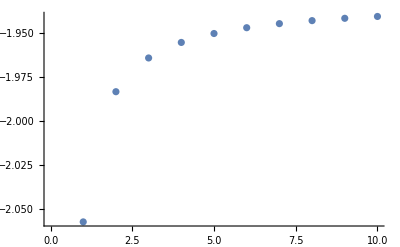

```mathematica
Table[((w ξ)/(h-z)+(z (h+2 w ξ) B0[h,w ξ,w ξ])/(2 (h-z)^2)-(z (h+2 w ξ) B0[z,w ξ,w ξ])/(2 (h-z)^2)+(w ξ (h+2 w ξ) C0[0,z,h,w ξ,w ξ,w ξ])/(h-z)) /.h->125/.z->91.1876/.w->80.385,{ξ,1,10}]
ListPlot[%]
```

#### cγZ finite part

```mathematica
Collect[resul0cγz/.w->gw^2 vev^2/4/.z->(g1^2+gw^2)vev^2/4,{ Subscript[A, αβ]^hγγ,C0[___],B0[___],Log[_]},Simplify]//.(g1^2+gw^2) vev^2->4z//.gw^2 vev^2->4w
```

(1/4 (g1^2+gw^2-(4 h)/vev^2)-(3 lam (-4 h+20 z) B0[h,h,h])/(-4 h+4 z)+((g1^2+gw^2) (3 h+4 z) B0[h,z,z])/(-4 h+4 z)+(-2 lam-(gw^2 ξ)/2) B0[h,w ξ,w ξ]+1/4 (-4 lam-(g1^2+gw^2) ξ) B0[h,z ξ,z ξ]-(2 (2 h^2+(g1^2+gw^2) (g1^2+gw^2-6 lam) vev^4-4 h z) B0[z,h,z])/(-4 h vev^2+(g1^2+gw^2) vev^4)-12 lam z C0[0,z,h,h,z,h]-1/8 (g1^2+gw^2) (8 h+12 z) C0[0,z,h,z,h,z]+(2 h (-2 h+4 z) Log[h])/(-4 h vev^2+(g1^2+gw^2) vev^4)-((g1^2+gw^2) (-2 h+4 z) Log[z])/(2 (-4 h+4 z))) A_αβ^hγγ

### tests

#### old test

```mathematica
Collect[Collect[(-gw^2/(z EL^2)Coefficient[result0AZ,g^αβ cW]+Coefficient[resul0cw,Subscript[A, αβ]^hγγ])/.w->gw^2 vev^2/4/.z->(g1^2+gw^2)vev^2/4,{C0[___],B0[___],Log[_]},Simplify]//.(g1^2+gw^2) vev^2->4z//.gw^2 vev^2->4w//PowerExpand,{C0[___],B0[___],Log[_]},Simplify]
Collect[Collect[(2/z Coefficient[result0AZ,g^αβ cW]+Coefficient[resul0cw,Subscript[A, αβ]^hγγ])/.w->gw^2 vev^2/4/.z->(g1^2+gw^2)vev^2/4,{C0[___],B0[___],Log[_]},Simplify]//.(g1^2+gw^2) vev^2->4z//.gw^2 vev^2->4w//PowerExpand,{C0[___],B0[___],Log[_]},Simplify]
```

(gw (52 gw^2 h+19 g1^4 vev^2-103 gw^4 vev^2+g1^2 (-76 h+24 gw^2 vev^2)))/(36 g1 (h-z))+(gw^3 (g1^2-5 gw^2) (g1^2+gw^2) vev^4 B0[h,w,w])/(8 g1 (h-z)^2)+(8 gw (5 g1^2-3 gw^2) (2 t+z) B0[z,t,t])/(9 g1 (g1^2+gw^2) vev^2)+1/(96 g1 (g1^2+gw^2) (h-z)^2)gw (g1^8 vev^4+g1^6 (-8 h vev^2+30 gw^2 vev^4)+g1^2 (640 gw^2 h^2-824 gw^4 h vev^2+274 gw^6 vev^4)+3 gw^4 (336 h^2+41 gw^4 vev^4-672 h w)+4 g1^4 (4 h^2+45 gw^4 vev^4-328 h w)) B0[z,w,w]+(gw^3 (16 h^2-4 (g1^2+5 gw^2) h vev^2+3 gw^2 (g1^2+3 gw^2) vev^4) C0[0,z,h,w,w,w])/(g1 (-4 h+4 z))+(16 gw (5 g1^2-3 gw^2) t Log[t])/(9 g1 (g1^2+gw^2) vev^2)-(2 gw^3 (g1^2-5 gw^2) Log[w])/(3 g1 (g1^2+gw^2))

(8 EL^2 (h-z) (38 g1^2+gw^2 (-23-6 ξ+3 ξ^2))-3 gw^4 (-4 h (-1+ξ)^2+vev^2 (g1^2 (-11-2 ξ+ξ^2)+gw^2 (61-2 ξ+ξ^2))))/(72 g1 gw (h-z))+(gw^3 (g1^2-5 gw^2) (g1^2+gw^2) vev^4 B0[h,w,w])/(8 g1 (h-z)^2)-(16 EL^2 (5 g1^2-3 gw^2) (2 t+z) B0[z,t,t])/(9 g1 gw (g1^2+gw^2) vev^2)+1/(192 g1 gw^3 (g1^2+gw^2) (h-z)^2)(gw^2 (g1^2+gw^2) (g1^8 vev^4+g1^6 (-8 h vev^2+22 gw^2 vev^4)+2 g1^2 (160 gw^2 h^2-188 gw^4 h vev^2+85 gw^6 vev^4)+3 gw^4 (144 h^2+49 gw^4 vev^4-288 h w)+4 g1^4 (4 h^2+11 gw^4 vev^4-168 h w))+32 EL^2 (g1^6+19 g1^4 gw^2-33 g1^2 gw^4-99 gw^6) (h-z)^2) B0[z,w,w]-((2 EL^2+gw^2) (g1^4-2 g1^2 gw^2 (-6+ξ)+gw^4 (12-4 ξ+ξ^2)) B0[z,w,w ξ])/(6 g1 gw^3)+((2 EL^2+gw^2) (g1^2+3 gw^2) (g1^2+gw^2 (1-4 ξ)) B0[z,w ξ,w ξ])/(12 g1 gw^3)+(gw^3 (16 h^2-4 (g1^2+5 gw^2) h vev^2+3 gw^2 (g1^2+3 gw^2) vev^4) C0[0,z,h,w,w,w])/(g1 (-4 h+4 z))+(8 EL^2 (-(20 g1 t)/(9 gw)+(4 gw t)/(3 g1)) Log[t])/((g1^2+gw^2) vev^2)-(gw (gw^2 (g1^2+gw^2) (-3+2 ξ+ξ^2)+2 EL^2 (g1^2 (-7+2 ξ+ξ^2)+gw^2 (17+2 ξ+ξ^2))) Log[w])/(6 g1 (g1^2+gw^2))-((2 EL^2 gw+gw^3) ξ (3+ξ) Log[ξ])/(6 g1)

```mathematica
-z EL^2/gw^2/.z->(g1^2+gw^2)vev^2/4/.EL^2->(g1^2 gw^2)/(g1^2+gw^2)
w-z/.w->gw^2 vev^2/4/.z->(g1^2+gw^2)vev^2/4//Simplify
```

-1/4 g1^2 vev^2

-1/4 g1^2 vev^2

```mathematica
resul0cwbtot;
Collect[Collect[(-gw^2/(2z EL^2)Coefficient[result0AZ,g^αβ cWB]+Coefficient[resul0cwb+(vev gw)/g1 haast,Subscript[A, αβ]^hγγ])/.w->gw^2 vev^2/4/.z->(g1^2+gw^2)vev^2/4,{C0[___],B0[___],Log[_]},Simplify]//.(g1^2+gw^2) vev^2->4z//.gw^2 vev^2->4w//PowerExpand,{C0[___],B0[___],Log[_],ξ},Simplify]
```

-(gw (-11 g1^6 vev^2+53 gw^4 (gw^2-8 lam) vev^2+g1^4 (-221 gw^2+376 lam) vev^2+g1^2 gw^2 (256 t+(59 gw^2+240 lam) vev^2)))/(36 g1 (g1^2+gw^2) (g1^2+gw^2-8 lam) vev^2)-(g1 gw^3 ξ)/(g1^2+gw^2-8 lam)+(64 g1 gw^3 t B0[h,t,t])/(9 (g1^2+gw^2-8 lam)^2 vev^2)+1/(2 g1 gw (g1^2+gw^2-8 lam)^2)(g1^6 (gw^2+4 lam)+g1^4 (-13 gw^4+16 gw^2 lam-64 lam^2)-gw^2 (gw^6-96 gw^2 lam^2+256 lam^3)+g1^2 (-3 gw^6+28 gw^4 lam-96 gw^2 lam^2+256 lam^3)) B0[h,w,w]+((4 g1 gw (g1^2+gw^2) lam)/((g1^2+gw^2-8 lam)^2)+(g1 gw^3 (g1^2+gw^2) ξ)/((g1^2+gw^2-8 lam)^2)) B0[h,w ξ,w ξ]+(4 gw (-(16 g1^2 gw^2 t)/((g1^2+gw^2-8 lam)^2)-((5 g1^2-3 gw^2) (2 t+z))/(g1^2+gw^2)) B0[z,t,t])/(9 g1 vev^2)+1/(12 g1 (g1^2+gw^2) (g1^2+gw^2-8 lam)^2)gw (-7 g1^8-33 gw^8+g1^6 (54 gw^2-56 lam)+600 gw^6 lam-2688 gw^4 lam^2+8 g1^4 (3 gw^4+gw^2 lam+64 lam^2)+g1^2 (-70 gw^6+664 gw^4 lam-640 gw^2 lam^2)) B0[z,w,w]+(-(4 g1 gw (g1^2+gw^2) lam)/((g1^2+gw^2-8 lam)^2)-(g1 gw^3 (g1^2+gw^2) ξ)/((g1^2+gw^2-8 lam)^2)) B0[z,w ξ,w ξ]-(8 g1 gw^3 t (16 t+(g1^2+gw^2-8 lam) vev^2) C0[0,z,h,t,t,t])/(9 (g1^2+gw^2) (g1^2+gw^2-8 lam) vev^2)+(gw (-2 g1^8+g1^6 (gw^2+16 lam)+g1^4 (23 gw^4-40 gw^2 lam)-g1^2 (gw^6-16 gw^4 lam)+3 (gw^8-8 gw^6 lam)) vev^2 C0[0,z,h,w,w,w])/(8 g1 (g1^2+gw^2) (g1^2+gw^2-8 lam))+(-(2 g1 gw^3 lam vev^2 ξ)/(g1^2+gw^2-8 lam)-(g1 gw^5 vev^2 ξ^2)/(2 (g1^2+gw^2-8 lam))) C0[0,z,h,w ξ,w ξ,w ξ]+(8 gw (-5 g1^2+3 gw^2) t Log[t])/(9 g1 (g1^2+gw^2) vev^2)+((3 g1^4 gw+4 g1^2 gw^3-5 gw^5) Log[w])/(3 g1^3+3 g1 gw^2)

```mathematica
Collect[Collect[(-gw^2/(z EL^2)Coefficient[result0AZ,g^αβ cB])/.w->gw^2 vev^2/4/.z->(g1^2+gw^2)vev^2/4,{C0[___],B0[___],Log[_]},Simplify]//.(g1^2+gw^2) vev^2->4z//.gw^2 vev^2->4w//PowerExpand,{C0[___],B0[___],Log[_]},Simplify]
```

(-38 g1^2 gw+gw^3 (23+6 ξ-3 ξ^2))/(18 g1)+(8 gw (5 g1^2-3 gw^2) (2 t+z) B0[z,t,t])/(9 g1 (g1^2+gw^2) vev^2)-((g1^6+19 g1^4 gw^2-33 g1^2 gw^4-99 gw^6) B0[z,w,w])/(12 g1^3 gw+12 g1 gw^3)+((g1^4-2 g1^2 gw^2 (-6+ξ)+gw^4 (12-4 ξ+ξ^2)) B0[z,w,w ξ])/(6 g1 gw)-((g1^2+3 gw^2) (g1^2+gw^2 (1-4 ξ)) B0[z,w ξ,w ξ])/(12 g1 gw)+(16 gw (5 g1^2-3 gw^2) t Log[t])/(9 g1 (g1^2+gw^2) vev^2)+(gw^3 (g1^2 (-7+2 ξ+ξ^2)+gw^2 (17+2 ξ+ξ^2)) Log[w])/(6 g1 (g1^2+gw^2))+(gw^3 ξ (3+ξ) Log[ξ])/(6 g1)

```mathematica
Collect[resul0cγz+(Coefficient[HWF,ϵ,0]+2dv)Subscript[A, αβ]^hγγ//.B0simplify/.GaugeXi[_]->ξ/.w->gw^2 vev^2/4/.z->(g1^2+gw^2)vev^2/4,{Subscript[A, αβ]^hγγ,B0[___],C0[___],Log[_]},Simplify]//.(g1^2+gw^2) vev^2->4z//.gw^2 vev^2->4w
```

A_αβ^hγγ (-(3 lam (-4 h+20 z) B0[h,h,h])/(-4 h+4 z)+gw^2 B0[h,w,w]+((g1^2+gw^2) (2 h+12 z) B0[h,z,z])/(2 (-4 h+4 z))+(-2 lam+(gw^2 ξ)/2) B0[h,w ξ,w ξ]+1/4 (-4 lam+(g1^2+gw^2) ξ) B0[h,z ξ,z ξ]-(2 (2 h^2+(g1^2+gw^2) (g1^2+gw^2-6 lam) vev^4-4 h z) B0[z,h,z])/(-4 h vev^2+(g1^2+gw^2) vev^4)-12 lam z C0[0,z,h,h,z,h]-1/8 (g1^2+gw^2) (8 h+12 z) C0[0,z,h,z,h,z]+(2 (-2 h^2+h (g1^2+gw^2+12 lam) vev^2-3 (g1^2+gw^2) lam vev^4) Log[h])/(-4 h vev^2+(g1^2+gw^2) vev^4)+1/4 gw^2 (-2-(12 w)/h) Log[w]+((g1^2+gw^2) (-16 h^2+3 (g1^2+gw^2)^2 vev^4-24 h z) Log[z])/(8 h (4 h-4 z))-B0[h,t,t] yu[3,3]^2+(4 t Log[t] yu[3,3]^2)/h+(-8 h^2+4 h (g1^2+2 (gw^2+6 lam)) vev^2+g1^4 vev^4+2 g1^2 gw^2 vev^4+3 gw^4 vev^4-32 t vev^2 yu[3,3]^2)/(8 h vev^2))

#### pole test Rh dv

```mathematica
1/4 (-24 lam-g1^2 (2+ξ)-gw^2 (2+3 ξ)) //Expand
2Coefficient[corr,ϵ,-1]/.t-> yu[3,3]^2 vev^2/2//Expand
%+%%
```

-g1^2/2-gw^2/2-6 lam-(g1^2 ξ)/4-(3 gw^2 ξ)/4

(3 g1^2 h A_αβ^hγγ)/(8 lam vev^2)+(9 w A_αβ^hγγ)/vev^2+(g1^2 h ξ A_αβ^hγγ)/(8 lam vev^2)+(3 w ξ A_αβ^hγγ)/vev^2-A_αβ^hγγ yu[3,3]^2

-g1^2/2-gw^2/2-6 lam-(g1^2 ξ)/4-(3 gw^2 ξ)/4+(3 g1^2 h A_αβ^hγγ)/(8 lam vev^2)+(9 w A_αβ^hγγ)/vev^2+(g1^2 h ξ A_αβ^hγγ)/(8 lam vev^2)+(3 w ξ A_αβ^hγγ)/vev^2-A_αβ^hγγ yu[3,3]^2

```mathematica
Collect[-2Coefficient[result,ϵ,-1],{Subscript[A, αβ]^hγγ,cWB,cγZ,z,g^αβ},Expand]
-2(-8 t+(g1^2+3 gw^2) vev^2 (3+ξ))/(4 vev^2)/.t-> yu[3,3]^2 vev^2/2//Expand
resulte=Collect[%%+%Subscript[A, αβ]^hγγ cγZ/.Kinetic2 /.AA->0,{Subscript[A, αβ]^hγγ,cWB,cγZ,z,g^αβ},Expand]
```

(cWB (2 g1 gw-(4 gw^3)/g1-(4 g1 lam)/gw+(4 gw lam)/g1)+cγZ (g1^2+gw^2+12 lam+(g1^2 ξ)/2+(3 gw^2 ξ)/2)) A_αβ^hγγ

-(3 g1^2)/2-(9 gw^2)/2-(g1^2 ξ)/2-(3 gw^2 ξ)/2+2 yu[3,3]^2

A_αβ^hγγ (cWB (2 g1 gw-(4 gw^3)/g1-(4 g1 lam)/gw+(4 gw lam)/g1)+cγZ (-g1^2/2-(7 gw^2)/2+12 lam+2 yu[3,3]^2))

```mathematica
test=(-8 t+(g1^2+3 gw^2) vev^2 (3+ξ))/(4 vev^2 ϵ)-(2 t B0[h,t,t])/vev^2-(2 (h-2 w) B0[h,w,w])/vev^2-((h-2 z) B0[h,z,z])/vev^2+(2 (h+2 w ξ) B0[h,w ξ,w ξ])/vev^2+((h+2 z ξ) B0[h,z ξ,z ξ])/vev^2-1/(8 vev^2)(2 (g1^2+3 gw^2) vev^2 (-1+ξ)+36 h^2 DB0[h,h,h]+16 (h-4 t) t DB0[h,t,t]+8 (h^2+(3 gw^4 vev^4)/4-4 h w) DB0[h,w,w]+(4 h^2+3 (g1^2+gw^2)^2 vev^4-16 h z) DB0[h,z,z])-1/2 gw^2 Log[w]+1/4 (-g1^2-gw^2) Log[z]+1/2 gw^2 ξ Log[w ξ]+1/4 (g1^2+gw^2) ξ Log[z ξ];
```

```mathematica
test/2;
dv/.GaugeXi[Q]->ξ;
corr=Collect[(%+%%)Subscript[A, αβ]^hγγ/.h->2lam vev^2/.w->gw^2 vev^2/4/.z->(g1^2+gw^2)vev^2/4,{Subscript[A, αβ]^hγγ,B0[___],Log[___]},Simplify]//.(g1^2+gw^2) vev^2->4z//.gw^2 vev^2->4w//.lam vev^2->h/2
Collect[resul0cγz/.w->gw^2 vev^2/4/.z->(g1^2+gw^2)vev^2/4,{ Subscript[A, αβ]^hγγ,C0[___],B0[___],Log[_]},Simplify]//.(g1^2+gw^2) vev^2->4z//.gw^2 vev^2->4w
Collect[%+%%,{ Subscript[A, αβ]^hγγ,ϵ,C0[___],B0[___],Log[_]},Simplify]
```

A_αβ^hγγ (-(t B0[h,t,t])/vev^2+1/2 (gw^2-4 lam) B0[h,w,w]+1/4 (g1^2+gw^2-4 lam) B0[h,z,z]+(2 lam+(gw^2 ξ)/2) B0[h,w ξ,w ξ]+1/4 (4 lam+(g1^2+gw^2) ξ) B0[h,z ξ,z ξ]-3 lam Log[h]+1/16 gw^2 (-4-(3 gw^2)/lam) Log[w]-((g1^2+gw^2) (3 g1^2+3 gw^2+4 lam) Log[z])/(32 lam)+(t Log[t] yu[3,3]^2)/(lam vev^2)+1/(32 lam vev^2 ϵ)(6 g1^2 h-32 lam t+144 lam w+2 g1^2 h ϵ+g1^4 vev^2 ϵ+3 gw^4 vev^2 ϵ+96 lam^2 vev^2 ϵ+8 g1^2 w ϵ+48 lam w ϵ+2 g1^2 h ξ+48 lam w ξ-288 lam^3 vev^4 ϵ DB0[h,h,h]-64 lam (h/2-2 t) t ϵ DB0[h,t,t]-4 lam (3 gw^4-8 gw^2 lam+16 lam^2) vev^4 ϵ DB0[h,w,w]-6 g1^4 lam vev^4 ϵ DB0[h,z,z]-12 g1^2 gw^2 lam vev^4 ϵ DB0[h,z,z]-6 gw^4 lam vev^4 ϵ DB0[h,z,z]+16 g1^2 lam^2 vev^4 ϵ DB0[h,z,z]+16 gw^2 lam^2 vev^4 ϵ DB0[h,z,z]-32 lam^3 vev^4 ϵ DB0[h,z,z]-32 t ϵ yu[3,3]^2))

(1/4 (g1^2+gw^2-(4 h)/vev^2)-(3 lam (-4 h+20 z) B0[h,h,h])/(-4 h+4 z)+((g1^2+gw^2) (3 h+4 z) B0[h,z,z])/(-4 h+4 z)+(-2 lam-(gw^2 ξ)/2) B0[h,w ξ,w ξ]+1/4 (-4 lam-(g1^2+gw^2) ξ) B0[h,z ξ,z ξ]-(2 (2 h^2+(g1^2+gw^2) (g1^2+gw^2-6 lam) vev^4-4 h z) B0[z,h,z])/(-4 h vev^2+(g1^2+gw^2) vev^4)-12 lam z C0[0,z,h,h,z,h]-1/8 (g1^2+gw^2) (8 h+12 z) C0[0,z,h,z,h,z]+(2 h (-2 h+4 z) Log[h])/(-4 h vev^2+(g1^2+gw^2) vev^4)-((g1^2+gw^2) (-2 h+4 z) Log[z])/(2 (-4 h+4 z))) A_αβ^hγγ

A_αβ^hγγ ((g1^2 h (3+ξ)+8 lam (-2 t+3 w (3+ξ)))/(16 lam vev^2 ϵ)-(3 lam (h-5 z) B0[h,h,h])/(h-z)-(t B0[h,t,t])/vev^2+1/2 (gw^2-4 lam) B0[h,w,w]-((4 lam (h-z)+g1^2 (2 h+5 z)+gw^2 (2 h+5 z)) B0[h,z,z])/(4 (h-z))-(2 (2 h^2+(g1^2+gw^2) (g1^2+gw^2-6 lam) vev^4-4 h z) B0[z,h,z])/(-4 h vev^2+(g1^2+gw^2) vev^4)-12 lam z C0[0,z,h,h,z,h]-1/2 (g1^2+gw^2) (2 h+3 z) C0[0,z,h,z,h,z]+(-3 lam-(4 h (h-2 z))/(-4 h vev^2+(g1^2+gw^2) vev^4)) Log[h]+1/16 gw^2 (-4-(3 gw^2)/lam) Log[w]-((g1^2+gw^2) (4 lam (3 h-5 z)+3 g1^2 (h-z)+3 gw^2 (h-z)) Log[z])/(32 lam (h-z))+(t Log[t] yu[3,3]^2)/(lam vev^2)+1/(32 lam vev^2)(2 g1^2 h-32 h lam+g1^4 vev^2+3 gw^4 vev^2+8 g1^2 lam vev^2+8 gw^2 lam vev^2+96 lam^2 vev^2+8 g1^2 w+48 lam w-288 lam^3 vev^4 DB0[h,h,h]-32 lam (h-4 t) t DB0[h,t,t]-12 gw^4 lam vev^4 DB0[h,w,w]+32 gw^2 lam^2 vev^4 DB0[h,w,w]-64 lam^3 vev^4 DB0[h,w,w]-6 g1^4 lam vev^4 DB0[h,z,z]-12 g1^2 gw^2 lam vev^4 DB0[h,z,z]-6 gw^4 lam vev^4 DB0[h,z,z]+16 g1^2 lam^2 vev^4 DB0[h,z,z]+16 gw^2 lam^2 vev^4 DB0[h,z,z]-32 lam^3 vev^4 DB0[h,z,z]-32 t yu[3,3]^2))

#### pole test cγγ cγZ

```mathematica
Collect[2/z ResulteAZ Subscript[A, αβ]^hγγ/g^αβ,{Subscript[A, αβ]^hγγ,cγZ,cγγ},Simplify]
Collect[ResulteZZ Subscript[A, αβ]^hγγ/g^αβ,{Subscript[A, αβ]^hγγ,cγZ,cγγ},Simplify]
```

-(cγγ EL^2 (41 g1^2+19 gw^2) A_αβ^hγγ)/(3 g1 gw)

(cγZ EL^2 (-41 g1^4+19 gw^4) A_αβ^hγγ)/(12 g1^2 gw^2)

```mathematica
cγγ(-(41 g1^2)/6-(19 gw^2)/6)2sw cw Subscript[A, αβ]^hγγ/.sw->g1/(√(g1^2+gw^2))/.cw->gw/(√(g1^2+gw^2))//Simplify
cγZ(-(41 g1^2)/6-(19 gw^2)/6)(cw^2-sw^2) Subscript[A, αβ]^hγγ/.sw->g1/(√(g1^2+gw^2))/.cw->gw/(√(g1^2+gw^2))//Simplify
```

-(cγγ g1 gw (41 g1^2+19 gw^2) A_αβ^hγγ)/(3 (g1^2+gw^2))

(cγZ (g1^2-gw^2) (41 g1^2+19 gw^2) A_αβ^hγγ)/(6 (g1^2+gw^2))

```mathematica
(cγZ (-41 g1^4 z+19 gw^4 z))/(6 (g1^2+gw^2))/((cγZ (g1^2-gw^2) (41 g1^2+19 gw^2))/(6 (g1^2+gw^2)))/.z->(g1^2+gw^2)vev^2/4//Simplify
```

((g1^2+gw^2) (-41 g1^4+19 gw^4) vev^2)/(4 (g1^2-gw^2) (41 g1^2+19 gw^2))